```mathematica
perfectQ[n_]:=(2n==Total[Divisors[n]])
```

```mathematica
Select[Range[10000],perfectQ]
```

{6,28,496,8128}

```mathematica
primesToN[n_]:=Select[Range[n],PrimeQ]
primeTwinQ[n_]:=PrimeQ[n+2]
```

```mathematica
s1=Select[primesToN[1000],primeTwinQ];
Transpose[AppendTo[{s1},Plus[s1,2]]]
```

{{3,5},{5,7},{11,13},{17,19},{29,31},{41,43},{59,61},{71,73},{101,103},{107,109},{137,139},{149,151},{179,181},{191,193},{197,199},{227,229},{239,241},{269,271},{281,283},{311,313},{347,349},{419,421},{431,433},{461,463},{521,523},{569,571},{599,601},{617,619},{641,643},{659,661},{809,811},{821,823},{827,829},{857,859},{881,883}}

```mathematica
data1 = {{1,3},{2,5},{3,8},{4,13}};
Simplify[InterpolatingPolynomial[data1,x]]
```

1/6 (6+14 x-3 x^2+x^3)

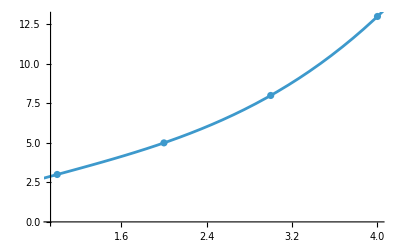

```mathematica
Show[ListPlot[data1],Plot[,{x, 0, 5}]]
```

```mathematica
Clear[x]
NDSolveValue[{x''[t]==-Sin[x[t]],x[0]==3.1,x'[0]==0},x[t],{t,0,20}]
NDSolveValue[{x''[t]==-Sin[x[t]],x[0]==3.2,x'[0]==0},x[t],{t,0,20}]
```

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

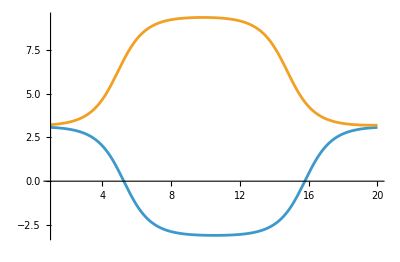

```mathematica
Plot[{,},{t,1,20},AspectRatio->Full]
```

```mathematica
NDSolveValue[{x'[t]==10(y[t]-x[t]),y'[t]==28x[t]-y[t]-z[t]*x[t],z'[t]==-8/3z[t]+x[t]*y[t],x[0]==5,y[0]==5,z[0]==5},{x[t],y[t],z[t]},{t,0,50}]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
ParametricPlot3D[,{t,0,50}]
```

-Graphics3D-

```mathematica
primeFibonacci[n_]:=Select[Fibonnaci[Range[]]]
```